```mathematica
Get["C:\\Users\\trste\\OneDrive\\Namizje\\3. Letnik\\5. semester\\napredna računalniška orodja\\2.Dn\\Pi_izracun.m"]
```

```mathematica
n=1000;(*poljubno stevilo tock*)
r=100;(*Radij kroznice*)
```

```mathematica
Tocke=Transpose[{RandomReal[{-r,r},n],RandomReal[{-r,r},n]}];
```

```mathematica
{notranje,zunanje}=Module[{TockeZnotraj,TockeZunaj,x,y,radiji},
TockeZnotraj={};
TockeZunaj={};

For[i=1,i<n,i++,
{x,y}=Tocke[[i]];
radiji=x^2+y^2;
If[radiji<r^2,AppendTo[TockeZnotraj,{x,y}],AppendTo[TockeZunaj,{x,y}]]];
{TockeZnotraj,TockeZunaj}];
```

```mathematica
krog=Graphics[{Red,Circle[{0,0},r]}];
okvir=Graphics[{EdgeForm[{Thick,Yellow}],FaceForm[],Rectangle[{-r,-r},{r,r}]}];
```

```mathematica
tocke=ListPlot[{zunanje,notranje},PlotMarkers->{Blue,Purple}];
```

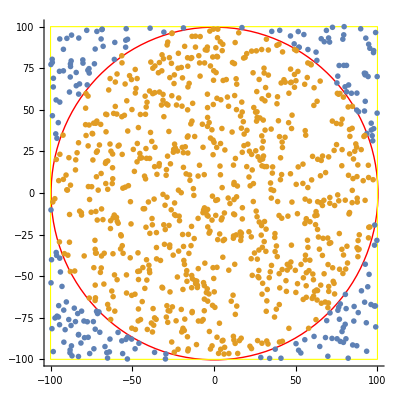

```mathematica
Show[{krog,okvir,tocke},Axes->True,AspectRatio->Automatic]
```

```mathematica
stevilopi=Izracun[notranje,n]
```

3.14

## RAZVOJ VRSTE Z TAYLORJEVO VRSTO

```mathematica
Clear[n]
```

```mathematica
Izris[ft_,{tMin_,tMax_}]:=Module[{f=ft,priblizek,Feksaktna,Faproksimativna},
Manipulate[aproksimacija=Normal[Series[f,{t,2,n}]];
Feksaktna=Plot[Evaluate[f],{t,tMin,tMax},PlotStyle->Blue,PlotLegends->{"Eksaktna funkcija"}];
Faproksimativna=Plot[Evaluate[aproksimacija],{t,tMin,tMax},PlotStyle->Red,PlotLegends->{"Aproksimacija po Taylor-ju"}];
Show[{Feksaktna,Faproksimativna},AxesLabel->{"t","f(t)"},PlotRange->All],{{n,2,"Stopnja polinoma"},0,10,1}]]
```

```mathematica
Izris[Sin[t]*t^2*Exp[-t],{0,4}]
```